```mathematica
SetDirectory["/home/anthony/Proyectos/Tropical/Code/tropical-geometry/Outputs"];
Import["/home/anthony/Proyectos/Tropical/Code/tropical-geometry/MathematicaCode/functions_TropGraph.wl"]
```

```mathematica
hf1= hyperPlanes["f1"];
bf1=bVec["f1"];
hull1 = extremalVert["f1"];
lf1 = lowerFaces["f1"];
```

```mathematica
Show[plotSubdiv[lf1,hull1],ViewPoint->{1,1,1}]
```

-Graphics3D-

```mathematica
Show[plotProjSub[lf1],ViewPoint->{0,0,10},Axes->False]
```

-Graphics3D-

```mathematica
hf2= hyperPlanes["f2"];
bf2=bVec["f2"];
hull2 = extremalVert["f2"];
lf2 = lowerFaces["f2"];
```

```mathematica
Show[plotSubdiv[lf2,hull2],ViewPoint->{1,1,1}]
```

-Graphics3D-

```mathematica
Show[plotProjSub[lf2],ViewPoint->Above]
```

-Graphics3D-

```mathematica
hf1f2=hyperPlanes["f1f2"];
bf1f2=bVec["f1f2"];
hull12=extremalVert["f1f2"];
lf12=lowerFaces["f1f2"];
```

```mathematica
Show[plotSubdiv[lf12, hull12],ViewPoint->{1,1,0}]
```

-Graphics3D-

```mathematica
Show[plotProjSub[lf12],ViewPoint->Above]
```

-Graphics3D-

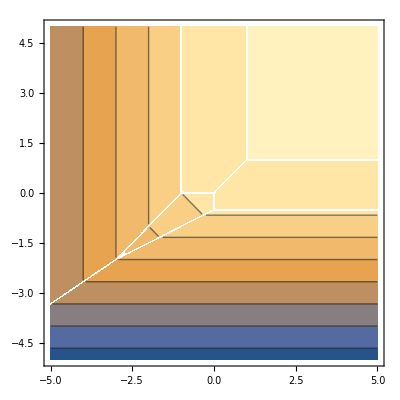

```mathematica
ContourPlot[Min[2x +2 ,x + y +1,x+ 1,2+ 3 y ,4+2y,1+y,2],{x,-5,5},{y,-5,5}]
```

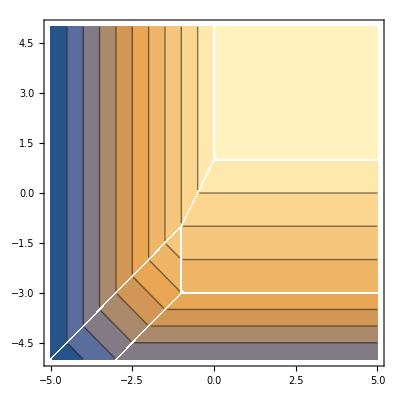

```mathematica
ContourPlot[Min[2+2x,2+x+y,4+2y,2+x,1+y,2],{x,-5,5},{y,-5,5}]
```

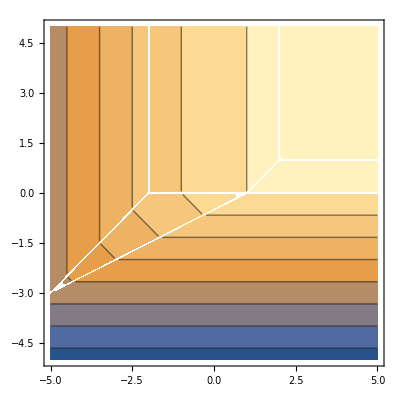

```mathematica
ContourPlot[Min[3+2x,1+x+y,2+3y,1+x,2+y,3],{x,-5,5},{y,-5,5}]
```